### Estimation parameters

```mathematica
capN=5
m=2
```

5

2

### Recursion for the coefficients of the integer valued polynomials

```mathematica
q[0]:=1;
q[s_]:=Product[x-k,{k,1,s}]/Factorial[s];
```

```mathematica
q[0,0]:=1;
q[0,m_]:=0;
q[s_,k_]:=q[s-1,k-1]/s- q[s-1,k];
```

```mathematica
q[0,0]
q[0,10]
q[0,-1]
q[4,-1]
Table[q[s,k],{s,0,5},{k,0,5}] //MatrixForm
Expand[q[0]]
Expand[q[1]]
Expand[q[2]]
Expand[q[3]]
Expand[q[4]]
Expand[q[5]]
```

1

0

0

0

(1 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0
1 | -3/2 | 1/2 | 0 | 0 | 0
-1 | 11/6 | -1 | 1/6 | 0 | 0
1 | -25/12 | 35/24 | -5/12 | 1/24 | 0
-1 | 137/60 | -15/8 | 17/24 | -1/8 | 1/120)

1

-1+x

1-(3 x)/2+x^2/2

-1+(11 x)/6-x^2+x^3/6

1-(25 x)/12+(35 x^2)/24-(5 x^3)/12+x^4/24

-1+(137 x)/60-(15 x^2)/8+(17 x^3)/24-x^4/8+x^5/120

### Coefficient of the discrete orthogonal polynomials

```mathematica
d[k_]:=Factorial[k]/Binomial[2*k,k]*Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s],{s,0,k}]
P[k_,i_]:=Factorial[k]/Binomial[2*k,k]*Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s,i],{s,0,k}];
```

```mathematica
Table[P[k,i],{k,0,5},{i,0,5}] //MatrixForm
Expand[d[0]]
Expand[d[1]]
Expand[d[2]]
Expand[d[3]]
Expand[d[4]]
Expand[d[5]]
```

(1 | 0 | 0 | 0 | 0 | 0
-3 | 1 | 0 | 0 | 0 | 0
7 | -6 | 1 | 0 | 0 | 0
-84/5 | 118/5 | -9 | 1 | 0 | 0
216/5 | -570/7 | 347/7 | -12 | 1 | 0
-120 | 274 | -225 | 85 | -15 | 1)

1

-3+x

7-6 x+x^2

-84/5+(118 x)/5-9 x^2+x^3

216/5-(570 x)/7+(347 x^2)/7-12 x^3+x^4

-120+274 x-225 x^2+85 x^3-15 x^4+x^5

### Cramer-Rao bounds

```mathematica
CRB[i_,snr_]:=Sum[Factorial[k]^(-2)*Binomial[2*k,k]*P[k,i]^2/Binomial[capN+k,2*k+1],{k,0,m}]/(2*snr);
ApproxCRB[i_,snr_]:=1/(2*capN^(2*i+1)*snr)*(1/(2*i+1)+(m+1)^2/(2*capN*(i+1)^2)-1/(2*capN))*((m+i+1)*Binomial[m+i,i]*Binomial[m,i])^2;
```

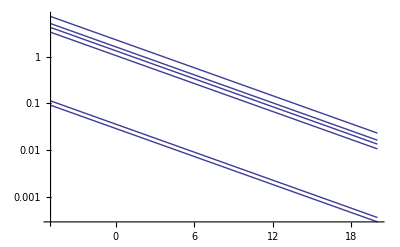

```mathematica
LogPlot[Flatten[Table[{CRB[i,10^(snrdb/10)],ApproxCRB[i,10^(snrdb/10)]},{i,0,m}]],{snrdb,-5,20}]
```

```mathematica
Table[{CRB[2,10^(snrdb/10)],ApproxCRB[2,10^(snrdb/10)]},{snrdb,-5,20}]
```

{{(√(5/2))/14,(18 √(2/5))/125},{5^(2/5)/(14 2^(3/5)),(18 2^(2/5))/(125 5^(3/5))},{5^(3/10)/(14 2^(7/10)),(18 2^(3/10))/(125 5^(7/10))},{5^(1/5)/(14 2^(4/5)),(18 2^(1/5))/(125 5^(4/5))},{5^(1/10)/(14 2^(9/10)),(18 2^(1/10))/(125 5^(9/10))},{1/28,18/625},{1/(28 10^(1/10)),(9 2^(9/10))/(625 5^(1/10))},{1/(28 10^(1/5)),(9 2^(4/5))/(625 5^(1/5))},{1/(28 10^(3/10)),(9 2^(7/10))/(625 5^(3/10))},{1/(28 10^(2/5)),(9 2^(3/5))/(625 5^(2/5))},{1/(28 √10),(9 √(2/5))/625},{1/(28 10^(3/5)),(9 2^(2/5))/(625 5^(3/5))},{1/(28 10^(7/10)),(9 2^(3/10))/(625 5^(7/10))},{1/(28 10^(4/5)),(9 2^(1/5))/(625 5^(4/5))},{1/(28 10^(9/10)),(9 2^(1/10))/(625 5^(9/10))},{1/280,9/3125},{1/(280 10^(1/10)),9/(3125 10^(1/10))},{1/(280 10^(1/5)),9/(3125 10^(1/5))},{1/(280 10^(3/10)),9/(3125 10^(3/10))},{1/(280 10^(2/5)),9/(3125 10^(2/5))},{1/(280 √10),9/(3125 √10)},{1/(280 10^(3/5)),9/(3125 10^(3/5))},{1/(280 10^(7/10)),9/(3125 10^(7/10))},{1/(280 10^(4/5)),9/(3125 10^(4/5))},{1/(280 10^(9/10)),9/(3125 10^(9/10))},{1/2800,9/31250}}

Plot the CRBs to a file

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/crbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[CRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{Directory[],"/Software/pubtex/polyphase_estimation/crbs/code/approxcrbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[ApproxCRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```